```mathematica
data =Import["D:\\学习\\大三下\\大物一级实验\\20170327 硅光电池特性研究\\作图.xlsx"]
```

{{{不同光照度下的P-R曲线(零偏）,},{负载R/Ω,功率P/mW},{L/lx,250.},{50.,0.0036992},{200.,0.0150152},{300.,0.022468},{400.,0.029757},{500.,0.0369376},{600.,0.0440646},{700.,0.0507065},{800.,0.0569245},{900.,0.0620944},{1000.,0.0663578},{2000.,0.0656306},{3000.,0.0514306},{4000.,0.0412902},{5000.,0.0343289},{6000.,0.0293021},{7000.,0.0255371},{8000.,0.0226313},{9000.,0.0202968},{10000.,0.0184041},{15000.,0.0125397},{20000.,0.0095048},{L/lx,111.},{50.,0.0007688},{200.,0.00320045},{300.,0.00481333},{400.,0.00642623},{500.,0.00801378},{600.,0.00965202},{700.,0.0112396},{800.,0.0128018},{900.,0.0143641},{1000.,0.015876},{2000.,0.029988},{3000.,0.0355123},{4000.,0.032418},{5000.,0.0283053},{6000.,0.0247812},{7000.,0.0219408},{8000.,0.0196218},{9000.,0.0177334},{10000.,0.0161765},{15000.,0.0111848},{20000.,0.00853258},{L/lx,62.5},{50.,0.000245},{200.,0.00102245},{300.,0.0015552},{400.,0.0020736},{500.,0.00260642},{600.,0.00312482},{700.,0.00365766},{800.,0.00416161},{900.,0.00468001},{1000.,0.00521284},{2000.,0.0102531},{3000.,0.0148263},{4000.,0.0183874},{5000.,0.0198198},{6000.,0.0192214},{7000.,0.0179225},{8000.,0.0165165},{9000.,0.0152111},{10000.,0.0140475},{15000.,0.0100104},{20000.,0.00775786},{L/lx,40.},{50.,0.0000882},{200.,0.000405},{300.,0.000616533},{400.,0.0008281},{500.,0.00103058},{600.,0.00124215},{700.,0.00145373},{800.,0.0016562},{900.,0.0018769},{1000.,0.00208849},{2000.,0.00416785},{3000.,0.0061744},{4000.,0.00803712},{5000.,0.0105065},{6000.,0.0109654},{7000.,0.0117834},{8000.,0.0119893},{9000.,0.0117723},{10000.,0.0113367},{15000.,0.00875075},{20000.,0.00692292}}}

```mathematica
distance20 = data[[1]][[4;;24]]
distance30 = data[[1]][[26;;46]]
distance40 = data[[1]][[48;;68]]
distance50 = data[[1]][[70;;90]]
```

{{50.,0.0036992},{200.,0.0150152},{300.,0.022468},{400.,0.029757},{500.,0.0369376},{600.,0.0440646},{700.,0.0507065},{800.,0.0569245},{900.,0.0620944},{1000.,0.0663578},{2000.,0.0656306},{3000.,0.0514306},{4000.,0.0412902},{5000.,0.0343289},{6000.,0.0293021},{7000.,0.0255371},{8000.,0.0226313},{9000.,0.0202968},{10000.,0.0184041},{15000.,0.0125397},{20000.,0.0095048}}

{{50.,0.0007688},{200.,0.00320045},{300.,0.00481333},{400.,0.00642623},{500.,0.00801378},{600.,0.00965202},{700.,0.0112396},{800.,0.0128018},{900.,0.0143641},{1000.,0.015876},{2000.,0.029988},{3000.,0.0355123},{4000.,0.032418},{5000.,0.0283053},{6000.,0.0247812},{7000.,0.0219408},{8000.,0.0196218},{9000.,0.0177334},{10000.,0.0161765},{15000.,0.0111848},{20000.,0.00853258}}

{{50.,0.000245},{200.,0.00102245},{300.,0.0015552},{400.,0.0020736},{500.,0.00260642},{600.,0.00312482},{700.,0.00365766},{800.,0.00416161},{900.,0.00468001},{1000.,0.00521284},{2000.,0.0102531},{3000.,0.0148263},{4000.,0.0183874},{5000.,0.0198198},{6000.,0.0192214},{7000.,0.0179225},{8000.,0.0165165},{9000.,0.0152111},{10000.,0.0140475},{15000.,0.0100104},{20000.,0.00775786}}

{{50.,0.0000882},{200.,0.000405},{300.,0.000616533},{400.,0.0008281},{500.,0.00103058},{600.,0.00124215},{700.,0.00145373},{800.,0.0016562},{900.,0.0018769},{1000.,0.00208849},{2000.,0.00416785},{3000.,0.0061744},{4000.,0.00803712},{5000.,0.0105065},{6000.,0.0109654},{7000.,0.0117834},{8000.,0.0119893},{9000.,0.0117723},{10000.,0.0113367},{15000.,0.00875075},{20000.,0.00692292}}

```mathematica
f20 =Interpolation[distance20, InterpolationOrder->2]
f30 =Interpolation[distance30, InterpolationOrder->2]
f40 =Interpolation[distance40, InterpolationOrder->2]
f50 =Interpolation[distance50, InterpolationOrder->2]
```

InterpolatingFunction[{{50., 20000.}}, <>]

InterpolatingFunction[{{50., 20000.}}, <>]

InterpolatingFunction[{{50., 20000.}}, <>]

«1 more identical outputs»

```mathematica
Show[ListPlot[{distance20,distance30,distance40,distance50},PlotStyle->Black,PlotMarkers->{Style["X",10]}],
Plot[f20[x],{x,50,21000},PlotStyle->Black],
Plot[f30[x],{x,50,21000},PlotStyle->Black],
Plot[f40[x],{x,50,21000},PlotStyle->Black],
Plot[f50[x],{x,50,21000},PlotStyle->Black],
AxesLabel->{Style[data[[1]][[2]][[1]],15,Bold],Style[data[[1]][[2]][[2]],15,Bold]},
AxesStyle->Directive[Arrowheads[0.03],13],
PlotLabel->Style[data[[1]][[1]][[1]],18,FontFamily->"Adobe Fan Heiti Std",Bold],
PlotRange->{0,0.08},
ImageSize->{800,500}]
```

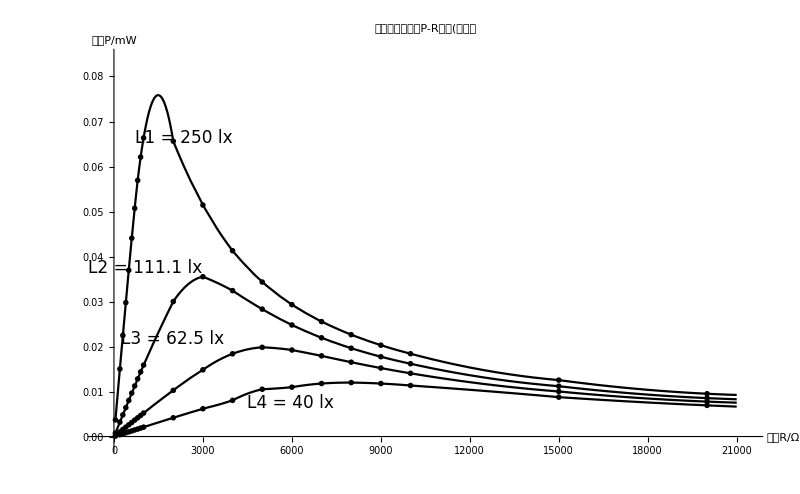

```mathematica
FindMaximum[f20[x],{x,1000}]
```

{0.0758523,{x→1490.78}}

```mathematica
FindMaximum[f30[x],{x,1000,20000}]
```

{0.0355123,{x→3000.}}

```mathematica
FindMaximum[f40[x],{x,1000,20000}]
```

{0.0198198,{x→5000.}}

```mathematica
FindMaximum[f50[x],{x,1000,20000}]
```

{0.0119893,{x→7986.81}}